# Correlating CFR and clade across states in the US

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/ncov-severity/across-states

## Clade proportion

```mathematica
strainToClade=Append[Map[#[[1]]->#[[2]]&,Drop[Import["strain_to_clade.tsv","TSV"],1]],_->""];
```

```mathematica
strainToClade[[1;;10]]
```

{Netherlands/NA_235/2020→G,Netherlands/NA_244/2020→G,Netherlands/NA_274/2020→G,Netherlands/NA_291/2020→G,Netherlands/NA_271/2020→G,Netherlands/NA_243/2020→G,Netherlands/NA_255/2020→G,Netherlands/NA_300/2020→G,Netherlands/NA_266/2020→G,Netherlands/NA_268/2020→G}

```mathematica
strainToState=Map[#[[1]]->#[[2]]&,Drop[Import["strain_to_state.tsv","TSV"],1]];
```

```mathematica
strainToState[[1;;10]]
```

{USA/AK-PHL003/2020→Alaska,USA/AK-PHL006/2020→Alaska,USA/AK-PHL015/2020→Alaska,USA/AK-PHL037/2020→Alaska,USA/AK-PHL077/2020→Alaska,USA/AK-PHL092/2020→Alaska,USA/AK-PHL101/2020→Alaska,USA/AK-PHL115/2020→Alaska,USA/AK-PHL118/2020→Alaska,USA/AZ-ASU2922/2020→Arizona}

```mathematica
Sort[Tally[strainToState[[All,2]]],#1[[2]]>#2[[2]]&]
```

{{Washington,878},{New York,610},{Wisconsin,172},{Arizona,83},{Minnesota,77},{Connecticut,67},{Virginia,59},{Utah,55},{California,41},{Idaho,32},{Diamond Princess,25},{Massachusetts,19},{Wyoming,16},{Illinois,15},{Georgia,15},{Oregon,10},{Pennsylvania,9},{Michigan,9},{Alaska,9},{Ohio,8},{North Carolina,8},{Florida,8},{South Carolina,7},{New Jersey,7},{Nebraska,7},{Iowa,7},{Indiana,6},{Grand Princess,6},{Texas,5},{Rhode Island,4},{New Hampshire,4},{Louisiana,3},{Nevada,2},{Maryland,2},{Hawaii,2},{Missouri,1},{Kansas,1},{District of Columbia,1}}

```mathematica
states=Sort[Tally[strainToState[[All,2]]],#1[[2]]>#2[[2]]&][[1;;10]][[All,1]]
```

{Washington,New York,Wisconsin,Arizona,Minnesota,Connecticut,Virginia,Utah,California,Idaho}

```mathematica
proportionInState[state_]:=Module[{cladeList},
cladeList=DeleteCases[Map[#/.strainToClade&,Cases[strainToState,x_/;x[[2]]==state][[All,1]]],""];
N[Count[cladeList,"G"]/Length[cladeList]]
]
```

```mathematica
proportionInState["Washington"]
```

0.352087

```mathematica
stateToCladeProportion=Map[#->proportionInState[#]&,states]
```

{Washington→0.352087,New York→0.912685,Wisconsin→0.755952,Arizona→0.841463,Minnesota→0.684211,Connecticut→0.712121,Virginia→0.745763,Utah→0.764706,California→0.30303,Idaho→0.967742}

## CFR

```mathematica
stateToAbbreviation=Map[#->Entity["AdministrativeDivision",{StringReplace[#," "->""],"UnitedStates"}][EntityProperty["AdministrativeDivision","StateAbbreviation"]]&,states]
```

{Washington→WA,New York→NY,Wisconsin→WI,Arizona→AZ,Minnesota→MN,Connecticut→CT,Virginia→VA,Utah→UT,California→CA,Idaho→ID}

```mathematica
cfrData=Import["covid_tracking_current.csv","CSV"];
```

```mathematica
MapIndexed[f,cfrData[[1]]]
```

{f[state,{1}],f[positive,{2}],f[positiveScore,{3}],f[negativeScore,{4}],f[negativeRegularScore,{5}],f[commercialScore,{6}],f[grade,{7}],f[score,{8}],f[negative,{9}],f[pending,{10}],f[hospitalizedCurrently,{11}],f[hospitalizedCumulative,{12}],f[inIcuCurrently,{13}],f[inIcuCumulative,{14}],f[onVentilatorCurrently,{15}],f[onVentilatorCumulative,{16}],f[recovered,{17}],f[lastUpdateEt,{18}],f[checkTimeEt,{19}],f[death,{20}],f[hospitalized,{21}],f[total,{22}],f[totalTestResults,{23}],f[posNeg,{24}],f[fips,{25}],f[dateModified,{26}],f[dateChecked,{27}],f[notes,{28}],f[hash,{29}]}

```mathematica
cfrData=Drop[cfrData,1];
```

```mathematica
Cases[cfrData,x_/;x[[1]]=="WA"][[1,2]]
```

11790

```mathematica
Cases[cfrData,x_/;x[[1]]=="WA"][[1,20]]
```

634

```mathematica
cfrForState[state_]:=Module[{abbreviation,cases,deaths},
abbreviation=state/.stateToAbbreviation;
deaths=Cases[cfrData,x_/;x[[1]]==abbreviation][[1,20]];
cases=Cases[cfrData,x_/;x[[1]]==abbreviation][[1,2]];
N[deaths/cases]
]
```

```mathematica
stateToCFR=Map[#->cfrForState[#]&,states]
```

{Washington→0.0537744,New York→0.0571244,Wisconsin→0.0506213,Arizona→0.0373301,Minnesota→0.0568761,Connecticut→0.0627436,Virginia→0.0333704,Utah→0.00879765,California→0.03844,Idaho→0.0269139}

## Plot

```mathematica
pairs=Map[{#/.stateToProportion,#/.stateToCFR}&,states]
```

{{0.352087,0.0537744},{0.912685,0.0571244},{0.755952,0.0506213},{0.841463,0.0373301},{0.684211,0.0568761},{0.712121,0.0627436},{0.745763,0.0333704},{0.764706,0.00879765},{0.30303,0.03844},{0.967742,0.0269139}}

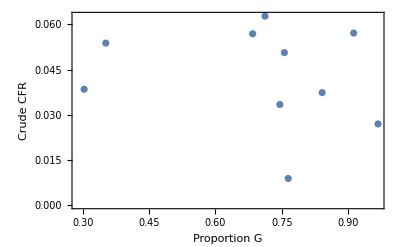

```mathematica
fig=ListPlot[pairs,PlotTheme->"FullAxes",FrameLabel->{"Proportion G","Crude CFR"}]
```

```mathematica
Export["figures/proportion_vs_cfr.png",fig,"PNG",ImageResolution->200]
```

figures/proportion_vs_cfr.png